```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.5.1/2.5.1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.5.1/f1.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.5.1/f2.xlsx,/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.5.1/~$2.5.1.xlsx}

```mathematica
file1 = files⟦2⟧
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.5.1/f1.xlsx

```mathematica
(s1 = Import[file1])//TableForm
```

T
sigma
в | 299.6
64.4413
1.54748 | 305.4
62.9813
1.51584 | 310.3
61.9384
1.49119 | 315.3
60.0612
1.44681 | 320.2
58.3926
1.4128 | 325.2
56.5154
1.36017 | 330.
54.0124
1.31413

```mathematica
s1 = s1⟦1⟧
```

{{T,sigma,в},{299.6,64.4413,1.54748},{305.4,62.9813,1.51584},{310.3,61.9384,1.49119},{315.3,60.0612,1.44681},{320.2,58.3926,1.4128},{325.2,56.5154,1.36017},{330.,54.0124,1.31413}}

```mathematica
s1⟦All, 1;;⟧
```

{{T,sigma,в},{299.6,64.4413,1.54748},{305.4,62.9813,1.51584},{310.3,61.9384,1.49119},{315.3,60.0612,1.44681},{320.2,58.3926,1.4128},{325.2,56.5154,1.36017},{330.,54.0124,1.31413}}

```mathematica
s1 = s1 ⟦2;;All⟧
```

{{299.6,64.4413,1.54748},{305.4,62.9813,1.51584},{310.3,61.9384,1.49119},{315.3,60.0612,1.44681},{320.2,58.3926,1.4128},{325.2,56.5154,1.36017},{330.,54.0124,1.31413}}

```mathematica
s1⟦All, 1;;2⟧
```

{{299.6,64.4413},{305.4,62.9813},{310.3,61.9384},{315.3,60.0612},{320.2,58.3926},{325.2,56.5154},{330.,54.0124}}

```mathematica
s2 = s1⟦All,1;;2⟧
```

{{299.6,64.4413},{305.4,62.9813},{310.3,61.9384},{315.3,60.0612},{320.2,58.3926},{325.2,56.5154},{330.,54.0124}}

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
error=ErrorBar/@s1⟦All, -1⟧
```

{ErrorBar[1.54748],ErrorBar[1.51584],ErrorBar[1.49119],ErrorBar[1.44681],ErrorBar[1.4128],ErrorBar[1.36017],ErrorBar[1.31413]}

```mathematica
Append[List[{1,2}],3]
```

{{1,2},3}

```mathematica
myerror = Append[List[s2⟦#⟧],error⟦#⟧] &/@Table[i,{i,Length@s2}]
```

{{{299.6,64.4413},ErrorBar[1.54748]},{{305.4,62.9813},ErrorBar[1.51584]},{{310.3,61.9384},ErrorBar[1.49119]},{{315.3,60.0612},ErrorBar[1.44681]},{{320.2,58.3926},ErrorBar[1.4128]},{{325.2,56.5154},ErrorBar[1.36017]},{{330.,54.0124},ErrorBar[1.31413]}}

```mathematica
line=LinearModelFit[s1⟦All, 1;;2⟧,{1,x},x]
line["ParameterTable"]
line= Normal[line]
```

FittedModel[166.492-0.338668 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 166.492 | 6.31426 | 26.3676 | 1.46649×10^-6
x | -0.338668 | 0.020026 | -16.9114 | 0.0000132211

166.492-0.338668 x

{ErrorBar[1.54748],ErrorBar[1.51584],ErrorBar[1.49119],ErrorBar[1.44681],ErrorBar[1.4128],ErrorBar[1.36017],ErrorBar[1.31413]}

```mathematica
s1
```

{{299.6,64.4413,ErrorBar[1.54748]},{305.4,62.9813,ErrorBar[1.51584]},{310.3,61.9384,ErrorBar[1.49119]},{315.3,60.0612,ErrorBar[1.44681]},{320.2,58.3926,ErrorBar[1.4128]},{325.2,56.5154,ErrorBar[1.36017]},{330.,54.0124,ErrorBar[1.31413]}}

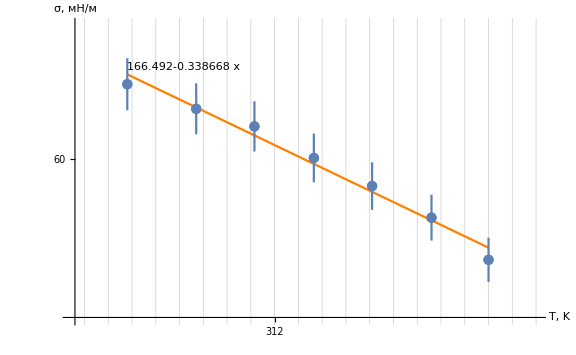

```mathematica
Show[
ListPlot[s1⟦All, 1;;2⟧,
AxesLabel->{Style["T, K",Medium],Style["σ, мН/м",Medium]},
AxesStyle->Directive[Arrowheads[{0.025}],Black], 
ImageSize->Large,GridLines->{Range[296,400,2], Range[0,70,1]},
Ticks-> {Range[200,400,4],Range[0,80,2]}, 
PlotRange->{{295,334},{50.5,68}}], 
Plot[line,{x,s1⟦1,1⟧,s1⟦-1,1⟧}, 
PlotLabels->Placed[line,Above],
PlotStyle->Orange],
ErrorListPlot[myerror]
]
```

```mathematica
file2 = files⟦3⟧
```

/Volumes/GoogleDrive/Мой диск/!МФТИ/Сollective intelligence 827/Лабы/2.5.1/f2.xlsx

```mathematica
(s3 = Import[file2])//TableForm
```

T
d
d
d
d | 299.6
101.465
6.44671
165.906
10.5411 | 305.4
103.429
6.57364
166.41
10.5765 | 310.3
105.089
6.6794
167.027
10.6162 | 315.3
106.782
6.78758
166.843
10.6054 | 320.2
108.441
6.89742
166.834
10.6115 | 325.2
110.135
6.9998
166.65
10.5917 | 330.
111.76
7.11429
165.773
10.5525

```mathematica
s3 = s3⟦1⟧
```

{{T,d,d,d,d},{299.6,101.465,6.44671,165.906,10.5411},{305.4,103.429,6.57364,166.41,10.5765},{310.3,105.089,6.6794,167.027,10.6162},{315.3,106.782,6.78758,166.843,10.6054},{320.2,108.441,6.89742,166.834,10.6115},{325.2,110.135,6.9998,166.65,10.5917},{330.,111.76,7.11429,165.773,10.5525}}

```mathematica
s3 = s3⟦2;;⟧
```

{{299.6,101.465,6.44671,165.906,10.5411},{305.4,103.429,6.57364,166.41,10.5765},{310.3,105.089,6.6794,167.027,10.6162},{315.3,106.782,6.78758,166.843,10.6054},{320.2,108.441,6.89742,166.834,10.6115},{325.2,110.135,6.9998,166.65,10.5917},{330.,111.76,7.11429,165.773,10.5525}}

```mathematica
data1 = s3⟦All,1;;3⟧
```

{{299.6,101.465,6.44671},{305.4,103.429,6.57364},{310.3,105.089,6.6794},{315.3,106.782,6.78758},{320.2,108.441,6.89742},{325.2,110.135,6.9998},{330.,111.76,7.11429}}

```mathematica
data2 = s3⟦All,{1,4,5}⟧
```

{{299.6,165.906,10.5411},{305.4,166.41,10.5765},{310.3,167.027,10.6162},{315.3,166.843,10.6054},{320.2,166.834,10.6115},{325.2,166.65,10.5917},{330.,165.773,10.5525}}

```mathematica
errordata1=ErrorBar/@data1⟦All, -1⟧
errordata2 = ErrorBar/@data2⟦All, -1⟧
```

{ErrorBar[6.44671],ErrorBar[6.57364],ErrorBar[6.6794],ErrorBar[6.78758],ErrorBar[6.89742],ErrorBar[6.9998],ErrorBar[7.11429]}

{ErrorBar[10.5411],ErrorBar[10.5765],ErrorBar[10.6162],ErrorBar[10.6054],ErrorBar[10.6115],ErrorBar[10.5917],ErrorBar[10.5525]}

```mathematica
data1 = data1⟦All,1;;2⟧
```

{{299.6,101.465},{305.4,103.429},{310.3,105.089},{315.3,106.782},{320.2,108.441},{325.2,110.135},{330.,111.76}}

```mathematica
data2 = data2⟦All,1;;2⟧
```

{{299.6,165.906},{305.4,166.41},{310.3,167.027},{315.3,166.843},{320.2,166.834},{325.2,166.65},{330.,165.773}}

```mathematica
myerrordata1 = Append[List[data1⟦#⟧],errordata1⟦#⟧] &/@Table[i,{i,Length@data1}]
myerrordata2 = Append[List[data2⟦#⟧],errordata2⟦#⟧] &/@Table[i,{i,Length@data2}]
```

{{{299.6,101.465},ErrorBar[6.44671]},{{305.4,103.429},ErrorBar[6.57364]},{{310.3,105.089},ErrorBar[6.6794]},{{315.3,106.782},ErrorBar[6.78758]},{{320.2,108.441},ErrorBar[6.89742]},{{325.2,110.135},ErrorBar[6.9998]},{{330.,111.76},ErrorBar[7.11429]}}

{{{299.6,165.906},ErrorBar[10.5411]},{{305.4,166.41},ErrorBar[10.5765]},{{310.3,167.027},ErrorBar[10.6162]},{{315.3,166.843},ErrorBar[10.6054]},{{320.2,166.834},ErrorBar[10.6115]},{{325.2,166.65},ErrorBar[10.5917]},{{330.,165.773},ErrorBar[10.5525]}}

```mathematica
linedata1=LinearModelFit[data1,{1,x},x]
linedata1["ParameterTable"]
linedata1= Normal[linedata1]
```

FittedModel[2.14303×10^-11+0.338668 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 2.14303×10^-11 | 9.56983×10^-12 | 2.23936 | 0.0752752
x | 0.338668 | 3.03512×10^-14 | 1.11583×10^13 | 1.09727×10^-64

2.14303×10^-11+0.338668 x

```mathematica
linedata2=LinearModelFit[data2,{},x]
linedata2["ParameterTable"]
linedata2= Normal[linedata2]
```

FittedModel[166.492]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 166.492 | 0.18378 | 905.93 | 1.22103×10^-16

166.492

```mathematica
Show[
ListPlot[data1,
AxesLabel->{Style["T, K",Medium],Style["мН/м",Medium]},
AxesStyle->Directive[Arrowheads[{0.025}],Black], 
ImageSize->Large,
GridLines->{Range[296,400,2], Range[0,210,5]},
Ticks-> {Range[200,400,4],Range[0,210,10]}, 
PlotRange->{{295,334},{40,190}}],
Plot[linedata1,{x,data1⟦1,1⟧,data1⟦-1,1⟧}, 
PlotLabels->Placed[{linedata1,Style["q",Medium]},{{Scaled[0.9],Above}, Scaled[0.45]}],
PlotStyle->Orange],
ErrorListPlot[myerrordata1],
ListPlot[data2],
Plot[linedata2,{x,data2⟦1,1⟧,data2⟦-1,1⟧}, 
PlotLabels->Placed[{linedata2, Style["U/F", Medium]},{{Scaled[0.95],Above}, Scaled[0.45]}],
PlotStyle->Orange],
ErrorListPlot[myerrordata2],
ListPlot[s1⟦All, 1;;2⟧,
AxesLabel->{Style["T, K",Medium],Style["σ, мН/м",Medium]},
AxesStyle->Directive[Arrowheads[{0.025}],Black], 
ImageSize->Large,GridLines->{Range[296,400,2], Range[0,70,1]},
Ticks-> {Range[200,400,4],Range[0,80,2]}, 
PlotRange->{{295,334},{50.5,68}}], 
Plot[line,{x,s1⟦1,1⟧,s1⟦-1,1⟧}, 
PlotLabels->Placed[{line, Style["σ", Medium]},{Above,Scaled[0.5]}],
PlotStyle->Orange],
ErrorListPlot[myerror]
]
```